```mathematica
dictionaryBackward[pairs_,nodes_]:=
Module[{n, new},
n = Length[pairs];
new = For[i=1,i≤n,i++, Sow[Sort[nodes[[pairs[[i]]]]]]]//Reap//Last//Last;
new];
distanceMatrix[points_]:=
Module[{n,distances},
n = Length[points];
distances = ConstantArray[1000,{n,n}];
For[i=1,i≤n,i++,For[j=1,j≤n,j++,distances[[i,j]] = EuclideanDistance[points[[i]],points[[j]]]]];
distances];

(* gives coordinates from flattened array to nonflattened *)
getpoints[loc_, n_]:=
Module[{a,b},
{a,b} = QuotientRemainder[loc +n,n];
If[b == 0,{a,b} = {a-1,b+n}];
{a,b}];
```

```mathematica
deleteduplicatepairs[pairs_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
Delete[pairs,todelete]];
```

```mathematica
modifiedEffectiveTransition[G_,k_]:=
Module[{M,spec,R,prediction, n, range,nodes,positions,cutoff},
nodes = VertexList[G];
n = VertexCount[G];
range = Range[n];
M=N[AdjacencyMatrix[G]];
spec=Max[Abs[Eigenvalues[M,1]]];
R=RandomReal[{0,1},{n,n}];
For[i=1,i≤n,i++,For[j=i+1,j≤n,j++,R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=2,i≤n,i++,
For[j=1,j≤i-1,j++, R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=1,i≤n,i++,
R[[i]][[i]]=0;];
cutoff = TakeLargest[Flatten[R-10M],2*k][[2*k]];
positions = deleteduplicatepairs[Position[R-10M,_?(#≥ cutoff&)]];
dictionaryBackward[positions,nodes]];
```

```mathematica
spectralEmbedPredictor[graph_,k_ ,dim_ :4]:=
Module[{L,evals,evecs,calculatedPoints, prediction,d, n, A},

(* Delete duplicate pairs and distances *)
deleteduplicates[pairs_, distances_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
{Delete[pairs,todelete], Delete[distances,todelete]}];

(* Compute all the distances and take the k smallest *)
brute[n_,points_, kval_,A_,original_] := 
Module[{dists, inds, indarr, row, temp, max,cut},
dists = distanceMatrix[points] ;
max = Max[dists] * 100.;
dists = dists + max * A + LowerTriangularize[ConstantArray[max, Dimensions[A]]];
If[original,cut=kval,cut=Min[Length[dists],kval]];
temp = Ordering[Flatten[dists], cut];
inds = Do[Sow[getpoints[p, n]], {p,temp}]//Reap//Last//Last;
{inds, Flatten[dists][[temp]]}];

(* Finds the k closest points to each point in points *)
allclosest[nval_,points_, l_, A_] :=
Module[{range,inds,dists, count},
count = l;
If[nval ≤ count,count = nval-1];
 range= Range[nval];
inds = Nearest[points->range,points,count+1][[All, Range[2,count+1]]];
calcdist[i_,j_]:=EuclideanDistance[points[[i]],points[[inds[[i,j]]]]] + 100*A[[i,inds[[i,j]]]];
dists = N[Array[calcdist, {nval,count}]];
{dists, inds, count}];

(* checks which nodes need to run through the program again *)
counter[n_,pairs_,points_,l_] := 
Module[{set, counts, mask, return},
set = DeleteDuplicates[pairs];
counts = Do[Sow[Count[pairs,x]],{x,set}]//Reap//Last//Last;
mask = For[i=1,i<Length[set]+1,i++,If[counts[[i]] ≥ l, Sow[set[[i]]]]]//Reap//Last;
If[mask === {}, return = {{},{}}, return = {points[[mask//Last]], mask//Last}];
return];

(* the actual heart of the function *)
continue[n_,points_,kval_,l_, L_,A_] := 
Module[{dists, inds, npairs, bestkinds, pairs,  pdists, S,mask, sclosest, sdists, count, temp},
{dists, inds, count} = allclosest[n,points,l + IntegerPart[Max[L]], A];
npairs = 2*kval;
bestkinds = Do[Sow[getpoints[p, count]], {p,Ordering[Flatten[dists], npairs]}]//Reap//Last//Last;
pairs = ConstantArray[0,{npairs, 2}];
pairs[[All,1]] = bestkinds[[All,1]];
pairs[[All,2]] = Do[Sow[inds[[bestkinds[[x,1]],bestkinds[[x,2]]]]],{x,npairs}]//Reap//Last//Last;
{S,mask} = counter[n,pairs[[All,1]], points, l];
pdists = Do[Sow[dists[[bestkinds[[x]][[1]],bestkinds[[x]][[2]]]]],{x, Length[bestkinds]}]//Reap//Last//Last;
{pairs, pdists} = deleteduplicates[pairs, pdists];
{sclosest, sdists} = If[Length[mask] > 1, closest[S,kval, L[[mask, mask]], A[[mask, mask]], False],{{},{}}];
temp = Do[Sow[mask[[sclosest[[i]]]]], {i,Length[sclosest]}]//Reap//Last;
If[temp === {}, pairs = pairs, pairs = Join[pairs, temp//Last]];
pdists = Join[pdists, sdists];
{pairs, pdists} = deleteduplicates[pairs, pdists];
{pairs,pdists}];

(* Check if k is such that it is just as fast to do brute force *)
closest[points_, kval_, L_,A_,original_]:=
Module[{nval, l},
nval = Length[points];
l = Ceiling[4*kval/N[nval]];
If[nval===0, {{},{}},If[(nval*nval) ≤ (4*kval)|| nval ≤ l, brute[nval, points, kval, A,original], continue[nval,points,kval,l, L,A]]]];

d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
(*{prediction,distances}  = closest[calculatedPoints, k, L,A,True];*)
{prediction, distances} = brute[n,calculatedPoints,k,A,True];
dictionaryBackward[prediction,VertexList[graph]]];
```

```mathematica
(* shortest path length predictor *)
shortestPathLength[g_,k_]:=
Module[{nodes, lengths, n, positions, prediction},
nodes = VertexList[g];
n = Length[nodes];
lengths = ConstantArray[100,{n,n}];
Do[lengths[[i,j]] = Length[FindShortestPath[g,nodes[[i]],nodes[[j]]]] - 1, {i,n-1},{j,i+1,n}];
lengths = lengths + 50*AdjacencyMatrix[g];
positions = Ordering[Flatten[lengths],k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* common neighbors predictor *)
commonNeighbors[g_,k_] :=
Module[{A,scores,n, positions,prediction},
A =AdjacencyMatrix[g];
n = Length[A];
scores = A.A + 1000*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[g]]];


(* preferential attatchment predictor *)
preferentialAttatchment[g_,k_]:=
Module[{degrees,A,n, scores, positions, prediction},
degrees = VertexDegree[g];
A =AdjacencyMatrix[g];
n = Length[A];
scores = Outer[Times,degrees,degrees]  + 1000*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[g]]];

(* katz predictor, beta .01 *)
katz[g_,k_] :=
Module[{spec,A, n, scores, positions, prediction,b},
A =AdjacencyMatrix[g];
spec=Max[Abs[Eigenvalues[A,1]]];
b = N[1/spec]-.001;
n = Length[A];
scores = Inverse[IdentityMatrix[n] - b * A] + 100*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[g]]];

jacard[g_,k_]:=
Module[{A,scores,n,d, positions,prediction, denominator},
A =AdjacencyMatrix[g];
d = VertexDegree[g];
n = Length[A];
scores = A.A ;
denominator = ConstantArray[0,{n,n}];
Do[denominator[[i,j]] = d[[i]]+d[[j]]-scores[[i,j]],{i,1,n},{j,1,n}];
scores = N[scores/denominator] + 1000*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[g]]];

(* page rank predictor, restart probability .1 *)
pageRank[g_, k_, restartProbability_ :.1]:=
Module[{A,n,degrees,scores, prediction, positions,p},
A =AdjacencyMatrix[g];
n = Length[A];
degrees = VertexDegree[g];
p = Transpose[N[Transpose[A]/degrees]];
scores = Inverse[IdentityMatrix[n] - restartProbability * p] +100*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[g]]];

(* moore penrose predictor *)
moorePenrose[g_,k_]:=
Module[{edgesKn, edgelist, edgecomp, c, L,M,score,positions, prediction,n},
edgesKn=Subsets[VertexList[g],{2}];edgelist=Apply[List,EdgeList[g],{1}];edgecomp=Complement[edgesKn,edgelist];c=Length[edgecomp];
L=KirchhoffMatrix[g];
M=PseudoInverse[L];
n = Length[L];
score={};Do[v=UnitVector[n,edgecomp[[i,1]]]-UnitVector[n,edgecomp[[i,2]]];s=v.M.v; score=AppendTo[score,s],{i,1,c}];
positions = Ordering[score,k];
prediction = Do[Sow[edgecomp[[i]]],{i,positions}]//Reap//Last//Last;
dictionaryBackward[prediction, VertexList[g]]];
```

```mathematica
getSum[graph_,x_,y_, rd_]:=
Module[{degrees, n, sum },
degrees = VertexDegree[graph];
n = Length[degrees];
sum = 0;
For[z=1,z≤n,z++,If[z≠x && z≠y,sum = sum + degrees[[z]]*(rd[[x,y]]+rd[[y,z]]-rd[[x,z]])]];
sum*.5];
```

```mathematica
(* Delete duplicate pairs and distances *)
deleteduplicates[pairs_, distances_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
{Delete[pairs,todelete], Delete[distances,todelete]}];
```

```mathematica
hittingTime[graph_,k_,dim_ :4]:=
Module[{L,evals,evecs,calculatedPoints, resdistances, scores, prediction,d, n, A, positions},
d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
resdistances = distanceMatrix[calculatedPoints];
scores=ConstantArray[100,{n,n}];
For[i=1,i< n, i++, For[j=i + 1,j≤ n,j++,scores[[i,j]] = getSum[graph,i,j,resdistances]]];
scores = scores + 1000*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction];
dictionaryBackward[prediction,VertexList[graph]]];


commuteTime[graph_,k_,dim_ :4]:=
Module[{L,evals,evecs,calculatedPoints, resdistances, scores, prediction,d, n, A, positions,HT},
d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
resdistances = distanceMatrix[calculatedPoints];
HT=ConstantArray[100,{n,n}];
For[i=1,i≤ n, i++, For[j= 1,j≤ n,j++,HT[[i,j]] = getSum[graph,i,j,resdistances]]];
scores = HT + Transpose[HT];
scores = scores + 1000*(A + IdentityMatrix[n]);
positions = Ordering[Flatten[scores],2*k];
prediction = Do[Sow[getpoints[loc,n]],{loc,positions}]//Reap//Last//Last;
prediction = deleteduplicatepairs[prediction][[1;;k]];
dictionaryBackward[prediction,VertexList[graph]]];
```

```mathematica
compareScoresFile[location_,name_] :=
Module[{data, lines, n, chop, train, test, k, toPredict, g,timeEffectiveTransition, predEffectiveTransition,scoreEffTransition,timeSpectralEmbedding, predSpectralEmbedding,scoreSpecEmbedding ,timeShortestPath, predShortestPath,scoreShortPath,timeCommonNeighbors, predCommonNeighbors,scoreCommNeighbors,timePrefAttatchment, predPrefAttatchment,scorePrefAttatchment,timeKatz, predKatz,scoreKatz,timePageRank, predPageRank,scorePageRank, timeHittingTime,predHittingTime,scoreHitTime,timeCommuteTime,predCommuteTime,scoreCommTime,results,table,timeJacard, predJacard,scoreJacard,predMoorePenrose, scoreMoorePenrose,timeMoorePenrose},
Print[name];
data = Import[location];
lines = StringSplit[data, "\n"];
lines = For[k=1,k≤Length[lines],k++,Sow[StringSplit[lines[[k]]]]]//Reap//Last//Last;
lines = For[k=1,k≤Length[lines],k++,Sow[{ToExpression[lines[[k]][[1]]],ToExpression[lines[[k]][[2]]],ToExpression[lines[[k]][[3]]]}]]//Reap//Last//Last;
lines = SortBy[lines,#[[3]]&];
n = Length[lines];
chop = Floor[3*n/4];
train = lines[[;;chop]];
(*train = Select[lines, #[[3]] == "0"&];*)
test = lines[[chop+1;;]];
k = Length[test];
Print[k];
toPredict = For[i = 1,i≤ k,i++,Sow[{test[[i]][[1]],test[[i]][[2]]}]]//Reap//Last//Last;
g = Graph[UndirectedEdge @@@ train, VertexLabels->"Name"];
Print[g];
{timeEffectiveTransition, predEffectiveTransition} = Timing[modifiedEffectiveTransition[g, k]];
Print[Length[predEffectiveTransition]];
scoreEffTransition = N[Length[Intersection[toPredict, predEffectiveTransition]]/Length[predEffectiveTransition]];
Print["Done With Effective Transition"];

{timeSpectralEmbedding, predSpectralEmbedding} = Timing[spectralEmbedPredictor[g,k]];
Print[Length[predSpectralEmbedding]];
scoreSpecEmbedding = N[Length[Intersection[toPredict, predSpectralEmbedding[[1]]]]/Length[predSpectralEmbedding[[1]]]];
Print["Done With Spectral Embedding"];

{timeShortestPath, predShortestPath} =  Timing[shortestPathLength[g,k]];
Print[Length[predShortestPath]];
scoreShortPath = N[Length[Intersection[toPredict, predShortestPath]]/Length[predShortestPath]];
Print["Done With Shortest Path"];

{timeCommonNeighbors, predCommonNeighbors} = Timing[commonNeighbors[g,k]];
Print[Length[predCommonNeighbors]];
scoreCommNeighbors = N[Length[Intersection[toPredict, predCommonNeighbors]]/Length[predCommonNeighbors]];
Print["Done With Common Neighbors"];

{timePrefAttatchment, predPrefAttatchment} = Timing[preferentialAttatchment[g,k]];
Print[Length[predPrefAttatchment]];
scorePrefAttatchment = N[Length[Intersection[toPredict, predPrefAttatchment]]/Length[predPrefAttatchment]];
Print["Done With Preferential Attatchment"];

{timeKatz, predKatz}= Timing[katz[g,k]];
Print[Length[predKatz]];
scoreKatz = N[Length[Intersection[toPredict, predKatz]]/Length[predKatz]];
Print["Done With Katz"];

{timeJacard, predJacard}= Timing[jacard[g,k]];
Print[Length[predJacard]];
scoreJacard = N[Length[Intersection[toPredict, predJacard]]/Length[predJacard]];
Print["Done With Jacard"];

{timePageRank, predPageRank} = Timing[pageRank[g,k]];
Print[Length[predPageRank]];
scorePageRank = N[Length[Intersection[toPredict, predPageRank]]/Length[predPageRank]];
Print["Done With Page Rank"];
(* TOO SLOW
{timeMoorePenrose, predMoorePenrose} = Timing[moorePenrose[g,k]];
scoreMoorePenrose = N[Length[Intersection[toPredict, predMoorePenrose]]/Length[predMoorePenrose]];
Print["Done With Moore Penrose"];
*)
{timeHittingTime, predHittingTime} = Timing[hittingTime[g,k]];
Print[Length[predHittingTime]];
scoreHitTime = N[Length[Intersection[toPredict, predHittingTime]]/Length[predHittingTime]];
Print["Done With Hitting Time"];

{timeCommuteTime, predCommuteTime} = Timing[commuteTime[g,k]];
Print[Length[predCommuteTime]];
scoreCommTime = N[Length[Intersection[toPredict, predCommuteTime]]/Length[predCommuteTime]];
Print["Done With Commute Time"];

results = {
{"Predictor", "Accuracy","Time"},
{"Effective Transition", scoreEffTransition, timeEffectiveTransition},
{"SpectralEmbedding", scoreSpecEmbedding,timeSpectralEmbedding},
{"ShortestPath", scoreShortPath,timeShortestPath},
{"CommonNeighbors", scoreCommNeighbors,timeCommonNeighbors},
{"PreferentialAttatchment", scorePrefAttatchment,timePrefAttatchment},
{"Katz", scoreKatz,timeKatz},
{"Jacard", scoreJacard,timeJacard},
{"PageRank", scorePageRank,timePageRank},
(*{"MoorePenrose",scoreMoorePenrose,timeMoorePenrose},*)
{"HittingTime",scoreHitTime,timeHittingTime},
{"CommuteTime", scoreCommTime,timeCommuteTime}
};
table = Grid[results, Alignment->Left, Spacings->{1, 1}, Frame->All, ItemStyle->"Text"];
Print[table];
table];
```

```mathematica
compareScoresRandom[g_,k_] :=
Module[{timeEffectiveTransition, predEffectiveTransition,lengthEffTransition,timeSpectralEmbedding, predSpectralEmbedding,lengthSpecEmbedding ,timeShortestPath, predShortestPath,lengthShortPath,timeCommonNeighbors, predCommonNeighbors,lengthCommNeighbors,timePrefAttatchment, predPrefAttatchment,lengthPrefAttatchment,timeKatz, predKatz,lengthKatz,timePageRank, predPageRank,lengthPageRank, timeHittingTime,predHittingTime,lengthHitTime,timeCommuteTime,predCommuteTime,lengthCommTime,results,table,timeJacard, predJacard,lengthJacard,predMoorePenrose, lengthMoorePenrose,timeMoorePenrose},
Print[g];
{timeEffectiveTransition, predEffectiveTransition} = Timing[modifiedEffectiveTransition[g, k]];
lengthEffTransition = Length[predEffectiveTransition];
Print["Done With Effective Transition"];

{timeSpectralEmbedding, predSpectralEmbedding} = Timing[spectralEmbedPredictor[g,k]];
lengthSpecEmbedding =Length[predSpectralEmbedding];
Print["Done With Spectral Embedding"];

{timeShortestPath, predShortestPath} =  Timing[shortestPathLength[g,k]];
lengthShortPath =Length[predShortestPath];
Print["Done With Shortest Path"];

{timeCommonNeighbors, predCommonNeighbors} = Timing[commonNeighbors[g,k]];
lengthCommNeighbors =Length[predCommonNeighbors];
Print["Done With Common Neighbors"];

{timePrefAttatchment, predPrefAttatchment} = Timing[preferentialAttatchment[g,k]];
lengthPrefAttatchment =Length[predPrefAttatchment];
Print["Done With Preferential Attatchment"];

{timeKatz, predKatz}= Timing[katz[g,k]];
lengthKatz =Length[predKatz];
Print["Done With Katz"];

{timeJacard, predJacard}= Timing[jacard[g,k]];
lengthJacard = Length[predJacard];
Print["Done With Jacard"];

{timePageRank, predPageRank} = Timing[pageRank[g,k]];
lengthPageRank =Length[predPageRank];
Print["Done With Page Rank"];

{timeMoorePenrose, predMoorePenrose} = Timing[moorePenrose[g,k]];
lengthMoorePenrose = Length[predMoorePenrose];
Print["Done With Moore Penrose"];

{timeHittingTime, predHittingTime} = Timing[hittingTime[g,k]];
lengthHitTime =Length[predHittingTime];
Print["Done With Hitting Time"];

{timeCommuteTime, predCommuteTime} = Timing[commuteTime[g,k]];
lengthCommTime = Length[predCommuteTime];
Print["Done With Commute Time"];

results = {
{"Predictor", "Prediction","Length","Time"},
{"Effective Transition",  predEffectiveTransition,lengthEffTransition, timeEffectiveTransition},
{"SpectralEmbedding", predSpectralEmbedding,lengthSpecEmbedding,timeSpectralEmbedding},
{"ShortestPath",predShortestPath, lengthShortPath,timeShortestPath},
{"CommonNeighbors",predCommonNeighbors, lengthCommNeighbors,timeCommonNeighbors},
{"PreferentialAttatchment",predPrefAttatchment, lengthPrefAttatchment,timePrefAttatchment},
{"Katz",predKatz, lengthKatz,timeKatz},
{"Jacard",predJacard, lengthJacard,timeJacard},
{"PageRank",predPageRank, lengthPageRank,timePageRank},
{"MoorePenrose",predMoorePenrose, lengthMoorePenrose,timeMoorePenrose},
{"HittingTime",predHittingTime,lengthHitTime,timeHittingTime},
{"CommuteTime",predCommuteTime, lengthCommTime,timeCommuteTime}
};
table = Grid[results, Alignment->Left, Spacings->{1, 1}, Frame->All, ItemStyle->"Text"];
Print[table];
table];
```

Hyper Text Data

549

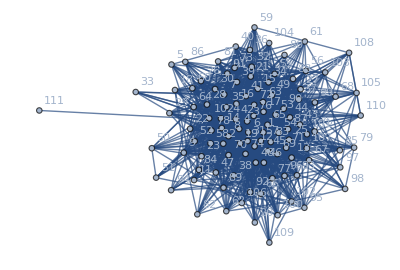

549

Done With Effective Transition

549

Done With Spectral Embedding

549

Done With Shortest Path

549

Done With Common Neighbors

549

Done With Preferential Attatchment

549

Done With Katz

549

Done With Jacard

549

Done With Page Rank

549

Done With Hitting Time

549

Done With Commute Time

Predictor | Accuracy | Time
Effective Transition | 0.10929 | 17.2876
SpectralEmbedding | 0. | 0.153005
ShortestPath | 0.105647 | 0.928889
CommonNeighbors | 0.0309654 | 0.014383
PreferentialAttatchment | 0.0309654 | 0.014269
Katz | 0.0382514 | 5.30318
Jacard | 0.0418944 | 0.250442
PageRank | 0.0418944 | 0.063097
HittingTime | 0.10929 | 3.23946
CommuteTime | 0.123862 | 5.04716

```mathematica
compareScoresFile["/Users/brynbb/Documents/link_prediction/data/hypertextdata.txt","Hyper Text Data"];
```

```mathematica
N[1098/2]
```

549.

Hyper Text Data

549

-Graphics-

549

Done With Effective Transition

549

Done With Spectral Embedding

549

Done With Shortest Path

549

Done With Common Neighbors

549

Done With Preferential Attatchment

549

Done With Katz

549

Done With Jacard

549

Done With Page Rank

549

Done With Hitting Time

549

Done With Commute Time

Predictor | Accuracy | Time
Effective Transition | 0.10929 | 17.4504
SpectralEmbedding | 0. | 0.15241
ShortestPath | 0.105647 | 1.33259
CommonNeighbors | 0.0309654 | 0.014793
PreferentialAttatchment | 0.0309654 | 0.014539
Katz | 0.0382514 | 5.51827
Jacard | 0.0418944 | 0.215524
PageRank | 0.0418944 | 0.067356
HittingTime | 0.10929 | 3.01346
CommuteTime | 0.123862 | 5.31863

Haggle Data

531

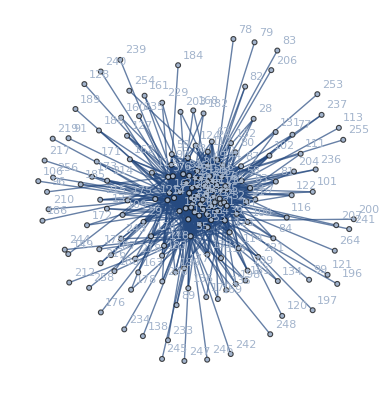

531

Done With Effective Transition

531

Done With Spectral Embedding

531

Done With Shortest Path

531

Done With Common Neighbors

531

Done With Preferential Attatchment

531

Done With Katz

531

Done With Jacard

531

Done With Page Rank

531

Done With Hitting Time

531

Done With Commute Time

Predictor | Accuracy | Time
Effective Transition | 0. | 64.6828
SpectralEmbedding | 0. | 0.092569
ShortestPath | 0.079096 | 0.752027
CommonNeighbors | 0.00188324 | 0.014112
PreferentialAttatchment | 0. | 0.015076
Katz | 0. | 30.2871
Jacard | 0.00188324 | 0.406352
PageRank | 0. | 0.065198
HittingTime | 0.0508475 | 9.85442
CommuteTime | 0.0885122 | 18.5559

Infectious Data

692

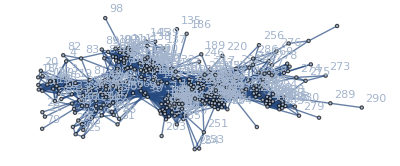

```mathematica
files = {
{"/Users/brynbb/Downloads/hypertextdata.txt","Hyper Text Data"}, 
{"/Users/brynbb/Downloads/haggledata.txt","Haggle Data"},
{"/Users/brynbb/Downloads/infectiousdata.txt", "Infectious Data"}
};

Do[compareScoresFile[file[[1]],file[[2]]], {file,files}]
```